```mathematica
da= 1/2 {{0.05, 0.1}, {0.05,-0.1},{-0.05, -0.1},{-0.05,0.1}}
```

{{0.025,0.05},{0.025,-0.05},{-0.025,-0.05},{-0.025,0.05}}

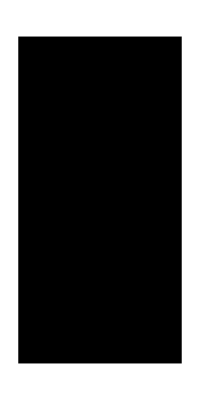

```mathematica
Polygon[%]//Graphics
```

```mathematica
dat=Composition[TranslationTransform[{0.15,0}],RotationTransform[ Pi/4],TranslationTransform[{0.05,0}]][da]
```

{{0.167678,0.0883883},{0.238388,0.0176777},{0.203033,-0.0176777},{0.132322,0.053033}}

```mathematica
dbt=Composition[TranslationTransform[{0.15,0}],RotationTransform[ Pi/4],TranslationTransform[{-0.05,0}]][da]
```

{{0.096967,0.0176777},{0.167678,-0.053033},{0.132322,-0.0883883},{0.0616117,-0.0176777}}

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/pbialas/PET/tools/src/2d/geometry

```mathematica
Export["gate_volume_test.txt", Join[dat, dbt], "Table"]
```

gate_volume_test.txt

```mathematica
LinearRepeat[poly_, ltr_, n_, v_]:= Module[{last = (n-1) v},
Composition[TranslationTransform[#],ltr][poly]&/@Table[v*i-last/2,{i,0,n-1}]
]
```

```mathematica
pr=LinearRepeat[da,TranslationTransform[{0,0}],4 , {0.1, 0.0}]
```

{{{-0.125,0.05},{-0.125,-0.05},{-0.175,-0.05},{-0.175,0.05}},{{-0.025,0.05},{-0.025,-0.05},{-0.075,-0.05},{-0.075,0.05}},{{0.075,0.05},{0.075,-0.05},{0.025,-0.05},{0.025,0.05}},{{0.175,0.05},{0.175,-0.05},{0.125,-0.05},{0.125,0.05}}}

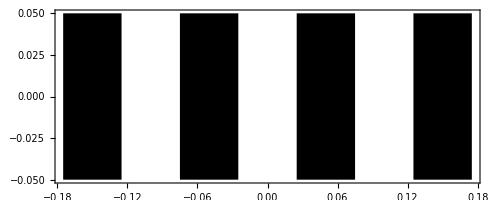

```mathematica
Graphics[Polygon/@pr, Frame->True]
```

```mathematica
Export["gate_volume_s_repeater_test.txt",Flatten[pr,1],"Table"]
```

gate_volume_s_repeater_test.txt

```mathematica
RingRepeat[poly_, ltr_, n_, angle_, center_: {0,0}]:= Module[{last = (n-1) v, t},
Composition[RotationTransform[#, center],ltr][poly]&/@Table[angle/n *i ,{i,0,n-1}]
]
```

```mathematica
rr=RingRepeat[da,TranslationTransform[{0,0.2}],5,2 Pi, {0.0, 0.0}]
```

{{{0.025,0.25},{0.025,0.15},{-0.025,0.15},{-0.025,0.25}},{{-0.230039,0.101031},{-0.134933,0.070129},{-0.150384,0.0225761},{-0.24549,0.0534778}},{{-0.167172,-0.18756},{-0.108393,-0.106658},{-0.0679424,-0.136047},{-0.126721,-0.216949}},{{0.126721,-0.216949},{0.0679424,-0.136047},{0.108393,-0.106658},{0.167172,-0.18756}},{{0.24549,0.0534778},{0.150384,0.0225761},{0.134933,0.070129},{0.230039,0.101031}}}

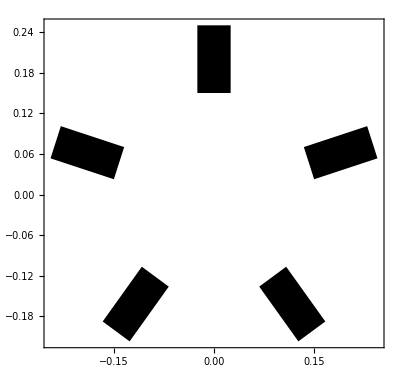

```mathematica
Graphics[Polygon/@rr, Frame->True]
```

```mathematica
Export["gate_volume_s_repeater_ring_test.txt",Flatten[rr,1],"Table"]
```

gate_volume_s_repeater_ring_test.txt

```mathematica
rr=RingRepeat[da,TranslationTransform[{0,0.2}],5,2 Pi, {0.2, 0.1}]
```

{{{0.025,0.25},{0.025,0.15},{-0.025,0.15},{-0.025,0.25}},{{0.00326355,-0.0200823},{0.0983692,-0.050984},{0.0829184,-0.0985369},{-0.0121873,-0.0676352}},{{0.25341,-0.124215},{0.312189,-0.0433133},{0.35264,-0.0727025},{0.293861,-0.153604}},{{0.429746,0.0815099},{0.370967,0.162412},{0.411418,0.191801},{0.470197,0.110899}},{{0.288581,0.312787},{0.193475,0.281886},{0.178024,0.329439},{0.27313,0.36034}}}

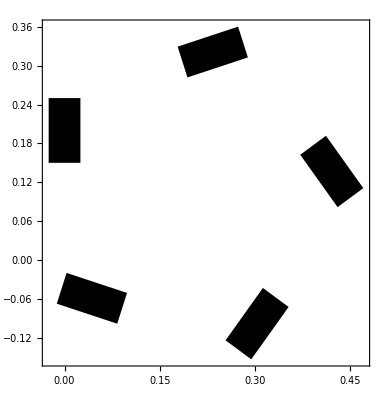

```mathematica
Graphics[Polygon/@rr, Frame->True]
```

```mathematica
Export["gate_volume_s_repeater_ring_off_test.txt",Flatten[rr,1],"Table"]
```

gate_volume_s_repeater_ring_off_test.txt

```mathematica
"gate_volume_s_repeater_ring_off_ test.txt"
```

gate_volume_s_repeater_ring_off_ test.txt